We begin by solving a matrix equation to get coefficients A, B, C, D, E, G. These coefficients allow us to get a stream function ψ from which the perpendicular force may be obtained

```mathematica
m={{a^4/10, -a/2, a^2, 1/a, 0, 0},{0, 0,0 ,0, a^4/10, a^2}, {2/5 a^3, -1/2, 2a, -1/a^2, -2/5a^3, -2a}, {2/5σ,σ/a^3,-2σ/a^2,4σ/a^5, -2/5, 2/a^2}, {1/(10ζ^4),-1/(2ζ),1/(ζ)^2, ζ,0,0}, {2/(5ζ^3),-1/2,2/ζ,-ζ^2,0, 0}};
b={{0},{0}, {0}, {0}, {1/2 U /ζ^2}, {U /ζ}};
Simplify[LinearSolve[m,b]//MatrixForm]
```

(-(5 a U ζ^3 (-3+3 a^2 ζ^2-2 σ))/((-1+a ζ)^3 (4 a^3 ζ^3 (-1+σ)+4 (1+σ)+3 a^2 ζ^2 (-1+2 σ)+3 a (ζ+2 ζ σ)))
-(2 a U (3+3 a^5 ζ^5 (-1+σ)+2 σ))/((-1+a ζ)^3 (4 a^3 ζ^3 (-1+σ)+4 (1+σ)+3 a^2 ζ^2 (-1+2 σ)+3 a (ζ+2 ζ σ)))
-(U (5 a^3 ζ^3+4 (1+σ)+3 a^5 ζ^5 (-3+2 σ)))/(2 (-1+a ζ)^3 (4 a^3 ζ^3 (-1+σ)+4 (1+σ)+3 a^2 ζ^2 (-1+2 σ)+3 a (ζ+2 ζ σ)))
-(U (a^3+a^6 ζ^3 (-1+σ)))/((-1+a ζ)^3 (4 a^3 ζ^3 (-1+σ)+4 (1+σ)+3 a^2 ζ^2 (-1+2 σ)+3 a (ζ+2 ζ σ)))
-(5 U (2+4 a ζ+6 a^2 ζ^2+3 a^3 ζ^3) σ)/(a^2 (-1+a ζ) (4 a^3 ζ^3 (-1+σ)+4 (1+σ)+3 a^2 ζ^2 (-1+2 σ)+3 a (ζ+2 ζ σ)))
(U (2+4 a ζ+6 a^2 ζ^2+3 a^3 ζ^3) σ)/(2 (-1+a ζ) (4 a^3 ζ^3 (-1+σ)+4 (1+σ)+3 a^2 ζ^2 (-1+2 σ)+3 a (ζ+2 ζ σ))))

We now have the value for the coefficient B. Show that in the limit of infinite interior viscosity and no rigidity that we get 3aU/2

```mathematica
B[a_,U_,ζ_,σ_ ]:=-(2 a U (3+3 a^5 ζ^5 (-1+σ)+2 σ))/((-1+a ζ)^3 (4 a^3 ζ^3 (-1+σ)+4 (1+σ)+3 a^2 ζ^2 (-1+2 σ)+3 a (ζ+2 ζ σ)))
Limit[B[a,U,ζ,0],ζ->0]
```

(3 a U)/2

```mathematica
TraditionalForm[B[a,U,ζ,σ]]
```

-(2 a U (3 a^5 ζ^5 (σ-1)+2 σ+3))/((a ζ-1)^3 (4 a^3 ζ^3 (σ-1)+3 a^2 ζ^2 (2 σ-1)+3 a (2 ζ σ+ζ)+4 (σ+1)))

We want to introduce λ, a quantity that is a/z, which will be our way to keep track of z.

```mathematica
B[a_,U_,λ_,θ_,σ_ ]:=-(2 a U (3+3 a^5 ζ^5 (-1+σ)+2 σ))/((-1+a ζ)^3 (4 a^3 ζ^3 (-1+σ)+4 (1+σ)+3 a^2 ζ^2 (-1+2 σ)+3 a (ζ+2 ζ σ)))/.{ζ->Cos[θ]λ/a}
Limit[B[a,U,λ,θ,0],λ->0]
TraditionalForm[Simplify[B[a,U,λ,θ,σ]]]
```

(3 a U)/2

-(2 a U (3 λ^5 (σ-1) cos^5(θ)+2 σ+3))/((λ cos(θ)-1)^3 (4 λ^3 (σ-1) cos^3(θ)+3 λ^2 (2 σ-1) cos^2(θ)+3 λ (2 σ+1) cos(θ)+4 (σ+1)))

```mathematica
Simplify[B[a,U,λ,θ,σ]]
```

```mathematica
-(2 a U (3+2 σ+3 λ^5 (-1+σ) Cos[θ]^5))/((-1+λ Cos[θ])^3 (4 (1+σ)+3 λ (1+2 σ) Cos[θ]+3 λ^2 (-1+2 σ) Cos[θ]^2+4 λ^3 (-1+σ) Cos[θ]^3))
```

Notice how a dependence is only implicit through λ and appears once in numerator

```mathematica
Manipulate[-3πμaU NIntegrate[(Sin[θ])^3
×-(2  (3+2 σ+3 λ^5 (-1+σ) Cos[θ]^5))/((-1+λ Cos[θ])^3 (4 (1+σ)+3 λ (1+2 σ) Cos[θ]+3 λ^2 (-1+2 σ) Cos[θ]^2+4 λ^3 (-1+σ) Cos[θ]^3)),{θ,0,π}],{λ,0,1},{σ,0,1}]
```

Make a plot of prefactor v. λ=a/z.

```mathematica
λmax=0.9;
Y0= {};
Do[res=With[{σ=0,ϵ=10^-9},-3 NIntegrate[(Sin[θ])^3
×-(2  (3+2 σ+3 λ^5 (-1+σ) Cos[θ]^5))/((-1+λ Cos[θ])^3 (4 (1+σ)+3 λ (1+2 σ) Cos[θ]+3 λ^2 (-1+2 σ) Cos[θ]^2+4 λ^3 (-1+σ) Cos[θ]^3)),{θ,ϵ,π-ϵ}]];AppendTo[Y0,res],{λ,0,λmax,0.01}]
X0 = Range[0,λmax,0.01];
Y1= {};
Do[res=With[{σ=1,ϵ=10^-9},-3 NIntegrate[(Sin[θ])^3
×-(2  (3+2 σ+3 λ^5 (-1+σ) Cos[θ]^5))/((-1+λ Cos[θ])^3 (4 (1+σ)+3 λ (1+2 σ) Cos[θ]+3 λ^2 (-1+2 σ) Cos[θ]^2+4 λ^3 (-1+σ) Cos[θ]^3)),{θ,ϵ,π-ϵ}]];AppendTo[Y1,res],{λ,0,λmax,0.01}]
Y2= {};
Do[res=With[{σ=0.5,ϵ=10^-9},-3 NIntegrate[(Sin[θ])^3
×-(2  (3+2 σ+3 λ^5 (-1+σ) Cos[θ]^5))/((-1+λ Cos[θ])^3 (4 (1+σ)+3 λ (1+2 σ) Cos[θ]+3 λ^2 (-1+2 σ) Cos[θ]^2+4 λ^3 (-1+σ) Cos[θ]^3)),{θ,ϵ,π-ϵ}]];AppendTo[Y2,res],{λ,0,λmax,0.01}]
```

```mathematica
L0= ListPlot[Transpose[{X0,Y0}],PlotStyle->Black,PlotLabels->"σ = 0"];
L1=ListPlot[Transpose[{X0,Y1}],PlotStyle->Red, PlotLabels->"σ = 1"];
L2=ListPlot[Transpose[{X0,Y2}],PlotStyle->Blue, PlotLabels->"σ = 0.5"];
Show[L0,L1,L2,AxesLabel->{"λ",Prefactor}]
```

-Graphics-

Make a plot of σ dependence for fixed σ

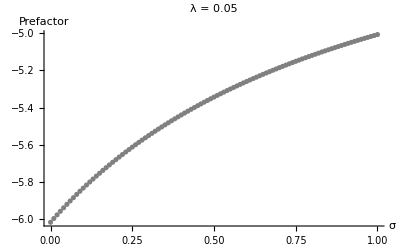

```mathematica
Y= {};
Do[res=With[{λ=0.05,ϵ=10^-9},-3 NIntegrate[(Sin[θ])^3
×-(2  (3+2 σ+3 λ^5 (-1+σ) Cos[θ]^5))/((-1+λ Cos[θ])^3 (4 (1+σ)+3 λ (1+2 σ) Cos[θ]+3 λ^2 (-1+2 σ) Cos[θ]^2+4 λ^3 (-1+σ) Cos[θ]^3)),{θ,ϵ,π-ϵ}]];AppendTo[Y,res],{σ,0,1,0.01}]
X = Range[0,1,0.01];
ListPlot[Transpose[{X,Y}],PlotStyle->Gray,AxesLabel->{σ,Prefactor},PlotLabel->"λ = 0.05"]
```

Make a 2D plot of prefactor in σ-λ parameter space

```mathematica
L ={};
Do[res=With[{ϵ=10^-9},-3 NIntegrate[(Sin[θ])^3
×-(2  (3+2 σ+3 λ^5 (-1+σ) Cos[θ]^5))/((-1+λ Cos[θ])^3 (4 (1+σ)+3 λ (1+2 σ) Cos[θ]+3 λ^2 (-1+2 σ) Cos[θ]^2+4 λ^3 (-1+σ) Cos[θ]^3)),{θ,ϵ,π-ϵ}]];AppendTo[L,res],{σ,0,1,0.01},{λ,0,0.5,0.005}]
```

```mathematica
A=ArrayReshape[L,{101,101}];
ArrayPlot[A,Mesh->None,ColorFunction->"BlueGreenYellow",FrameTicks->Automatic,FrameLabel->{"j (σ ∈ [0,1.])","i (λ ∈ [0,0.5])"},PlotLegends->Automatic,PlotLabel->"Prefactor in σ-λ space", DataReversed->True]
```